```mathematica
Quit[]
```

### linear slope

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]+F0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)-(F0 (-1+ⅇ^(3 H (-t+tc))+3 H (t-tc)))/(9 H^2)+xc

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

dxL+dotxL/(3 H)-(dotxL ⅇ^(3 H (-t+tL)))/(3 H)+xL+(F0 (1-3 H t+3 H tL-(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]))/(9 H^2)

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+ϵ xi0]==xSR[t]/.{dxL->ϵ dxL}]/.{tc->tcUSR}]
```

1/(9 H^2)(3 dotxL ⅇ^(3 H (-t+tL)) H-3 dotxL ⅇ^(-3 H (t-tL+xi0 ϵ)) H+(dotxL ⅇ^(3 H (-t+tL)) F0)/(dotxL-3 H xc+3 H xL)+9 dxL H^2 ϵ-3 F0 H xi0 ϵ-(dotxL ⅇ^(-3 H (t-tL+xi0 ϵ)) F0)/(dotxL+3 H (-xc+xL+dxL ϵ))-F0 Log[dotxL/(dotxL-3 H xc+3 H xL)]+F0 Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))])==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{ϵ,0,1}]]/.{ϵ->1}//Simplify
```

dxL+dotxL ⅇ^(3 H (-t+tL)) xi0+(dotxL ⅇ^(3 H (-t+tL)) F0 (dxL+xi0 (dotxL+3 H (-xc+xL))))/(3 H (dotxL+3 H (-xc+xL))^2)==(F0 (xi0+dxL/(dotxL+3 H (-xc+xL))))/(3 H)

```mathematica
xi0SR[t_]=xi0/.Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

(dxL (-dotxc F0+dotxL ⅇ^(3 H (-t+tL)) F0+3 dotxc^2 H))/(dotxc (-dotxL ⅇ^(3 H (-t+tL)) F0+dotxc (F0-3 dotxL ⅇ^(3 H (-t+tL)) H)))

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(dxL ⅇ^(3 H (-t+tc)) F0)/dotxc

```mathematica
Normal[Series[Simplify[xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->(ϵ F0)/(3H)}//Simplify,{ϵ,0,-1}]]/.{ϵ->(3H dotxc)/F0}//Simplify
```

(dxL ⅇ^(3 H (-t+tc)) F0)/dotxc

```mathematica
Simplify[xSR'[t]xi0SR'[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->(ϵ F0)/(3H)}//Simplify
```

-(3 dxL ⅇ^(3 H tc) H ϵ)/(-ⅇ^(3 H t)+ⅇ^(3 H tc) (1+ϵ))

```mathematica
Simplify[Normal[Series[xSR'[t]xi0SR'[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->(ϵ F0)/(3H)},{ϵ,0,1}]]]
```

(3 dxL ⅇ^(3 H tc) H ϵ)/(ⅇ^(3 H t)-ⅇ^(3 H tc))

```mathematica
Simplify[Normal[Series[xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->(ϵ F0)/(3H)},{ϵ,0,1}]]]
```

(3 dxL ⅇ^(3 H tc) H (-1+ⅇ^(3 H (-t+tc))+ϵ^2))/((-ⅇ^(3 H t)+ⅇ^(3 H tc)) ϵ)

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

-(dotxL ⅇ^(3 H (-t+tL)) F0)/dotxc^2

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

-(3 dotxc^2 ⅇ^(3 H (t-tL)) H)/(dotxL F0)

bispectrum correction reads

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->-dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-6 Ps zetaL

### quadratic slope

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-m^2(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tc)+3 H (-tc+tL)) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tc))))/(√(9 H^2+4 m^2))+xc

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc-1/(√(9 H^2+4 m^2))ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL-Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H))) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)))) (dotxL+3 H (dxL-xc+xL))

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+ϵ xi0]==xSR[t]/.{dxL->ϵ dxL}]/.{tc->tcUSR}]
```

1/(√(9 H^2+4 m^2))(ⅇ^(-1/2 (3 H+√(9 H^2+4 m^2)) (t-tL)) (dotxL-dotxL ⅇ^(√(9 H^2+4 m^2) (t-tL-Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) (dotxL/(dotxL-3 H xc+3 H xL))^(1/6 (-3+(√(9 H^2+4 m^2))/H))-ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL+xi0 ϵ-Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))]/(3 H))) (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL-xi0 ϵ+Log[dotxL/(dotxL+3 H (-xc+xL+dxL ϵ))]/(3 H)))) (dotxL+3 H (-xc+xL+dxL ϵ)))==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{ϵ,0,1}]]/.{ϵ->1}//Simplify
```

1/(√(9 H^2+4 m^2))ⅇ^(1/2 (-3 H+√(9 H^2+4 m^2)) (t-tL-Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H))) (3 dxL (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) H-dxL (1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) √(9 H^2+4 m^2)+(3 (-1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) H+(1+ⅇ^(√(9 H^2+4 m^2) (-t+tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)))) √(9 H^2+4 m^2)) xi0 (-dotxL+3 H (xc-xL)))==0

```mathematica
xi0SR[t_]=Simplify[Simplify[Simplify[xi0/.Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxc->dotxL Exp[-3H(tc-tL)]},{H>0,tc-tL>0}]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{H->(-Cp-Cm)/3}//Simplify
```

(dxL (-Cm+Cp ⅇ^((Cm-Cp) (t-tc))))/(dotxc (-Cp+Cm ⅇ^((Cm-Cp) (t-tc))))

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=Simplify[Simplify[xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]/.{dotxc->dotxL Exp[-3H(tc-tL)]}/.{H->(-Cp-Cm)/3}]
```

(Cm Cp dxL (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))))/(Cm-Cp)

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=Simplify[Simplify[D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}/.{dotxL->dotxc Exp[3H(tc-tL)]},{H>0,tc>tL}]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]
```

((ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)/(Cm-Cp)

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

(3 (Cm-Cp) H)/((ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)

zetaS can be understood as H xi0 with the replacement dxL→dxS

```mathematica
Limit[H xi0SR[t]/.{dxL->dxS},{t->∞},Assumptions->{Cp-Cm>0}]
```

(Cm dxS H)/(Cp dotxc)

Thus 𝒫_ζ_S=(C_-)^2/(C_+)^2 H^2/((ϕ̇)_c)^2(H/(2π))^2

bispectrum correction reads

```mathematica
ddotxcddxL/ddotxddxL(-2/dotxc Ps)
```

-(6 (Cm-Cp) H Ps)/(dotxc (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))) m^2)

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->Cp/Cm dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-(6 Cp^2 Ps zetaL)/m^2

```mathematica
Simplify[Normal[Series[(-3H+√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

m^2/(3 H)

### Suyama-san’s general formula

#### linear slope

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
Simplify[Solve[tc==tcUSR,xc],{tc>tL,H>0}][[1]]
```

{xc→(dotxL-dotxL ⅇ^(3 H (-tc+tL))+3 H xL)/(3 H)}

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]+F0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc]}
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)-(F0 (-1+ⅇ^(3 H (-t+tc))+3 H (t-tc)))/(9 H^2)+xc

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

dxL+dotxL/(3 H)-(dotxL ⅇ^(3 H (-t+tL)))/(3 H)+xL+(F0 (1-3 H t+3 H tL-(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]))/(9 H^2)

```mathematica
dotx[t_]=xUSR'[t](1-UnitStep[t-tc])+xSR'[t]UnitStep[t-tc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}//Simplify
```

dotxL ⅇ^(3 H (-t+tL))+((-1+ⅇ^(3 H (-t+tc))) F0 UnitStep[t-tc])/(3 H)

```mathematica
dotxbar[t_]=xbarUSR'[t](1-UnitStep[t-ttbarc])+xbarSR'[t]UnitStep[t-ttbarc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}//Simplify
```

(3 dotxL ⅇ^(-3 H t) H (dotxL ⅇ^(3 H tL)+3 dxL ⅇ^(3 H tc) H)+F0 (dotxL (-1+ⅇ^(3 H (-t+tc)))-3 dxL ⅇ^(3 H (tc-tL)) H) UnitStep[t-tL-Log[(dotxL ⅇ^(3 H tc))/(dotxL ⅇ^(3 H tL)+3 dxL ⅇ^(3 H tc) H)]/(3 H)])/(3 H (dotxL+3 dxL ⅇ^(3 H (tc-tL)) H))

```mathematica
xbarSR'[t]
```

dotxL ⅇ^(3 H (-t+tL))+(F0 (-3 H+(3 dotxL ⅇ^(3 H (-t+tL)) H)/(dotxL+3 H (dxL-xc+xL))))/(9 H^2)

```mathematica
xbarUSR'[ttbarc]-xUSR'[tcUSR]//Simplify
```

3 dxL H

```mathematica
Normal[Series[ttbarc-tcUSR,{dxL,0,1}]]//Simplify
```

-dxL/(dotxL+3 H (-xc+xL))

```mathematica
PlotParams={H->1,dotxL->10^-2,tL->0,tc->2,F0->-10^-3,dxL->-10^-7};
```

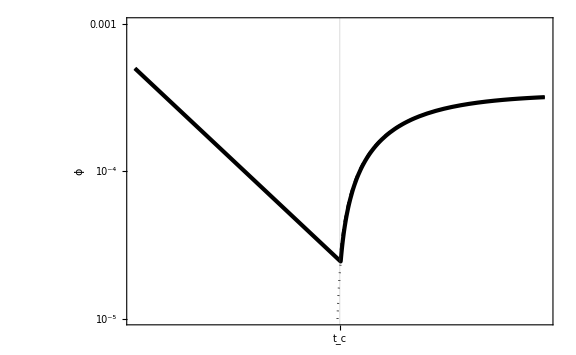

```mathematica
LogPlot[{dotx[t]/.PlotParams,
dotxbar[t]/.PlotParams,
xbarSR'[t]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams},{t,1,3},PlotStyle->{{Black,Dashed},{Black,AbsoluteThickness[3]},{Black,Dotted}},GridLines->{{2},None},PlotRange->{10^-5,10 10^-4},FrameTicks->{None,{{{2,"t_(<c>)"}},None}},FrameLabel->{None,ϕ̇}]
```

```mathematica
ttbarc/.PlotParams
```

1/3 Log[1/(100 (1/100+3 (-1/10000000-xc+xL)))]

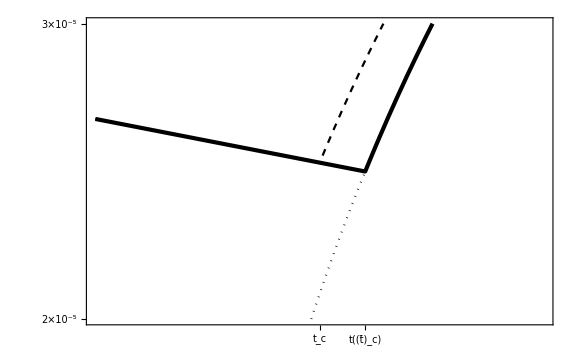

```mathematica
LogPlot[{dotx[t]/.PlotParams,
dotxbar[t]/.PlotParams,
xbarSR'[t]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams},{t,1.98,2.02},PlotStyle->{{Black,Dashed},{Black,AbsoluteThickness[3]},{Black,Dotted}},GridLines->{{2,ttbarc/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams},{dotx[2]/.PlotParams,dotxbar[ttbarc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,xbarSR'[2]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams}},PlotRange->{2 10^-5,3 10^-5},FrameTicks->{{{{dotx[2]/.PlotParams,Subscript[OverDot[ϕ], "c"]},{dotxbar[ttbarc]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,Subscript[OverDot[OverBar[ϕ]], "c"]},{xbarSR'[2]/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,OverDot[OverBar[ϕ]]["t_(<c>)"]}},None},{{{2,"t_(<c>)"},{ttbarc/.{xc->xL+dotxL(1-Exp[-3H(tc-tL)])/(3H)}/.PlotParams,Style["t",Italic][Subscript[OverBar[Style["t",Italic]], "c"]]}},None}}]
```

```mathematica
ZcIndet[t_]=Integrate[Exp[-3H (t-tc)]/xSR'[t]^2,t]
```

(3 ⅇ^(3 H tc) H)/(F0 (-ⅇ^(3 H t) F0+ⅇ^(3 H tc) F0+3 dotxL ⅇ^(3 H tL) H))

```mathematica
Limit[ZcIndet[t],{t->∞},Assumptions->{H>0}]
```

0

```mathematica
Zc=-ZcIndet[tc]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-1/(dotxc F0)

```mathematica
xSR''[t]// Simplify
```

-ⅇ^(-3 H t) (ⅇ^(3 H tc) F0+3 dotxL ⅇ^(3 H tL) H)

#### quadratic slope

```mathematica
Quit[]
```

```mathematica
xSR[t_]=Simplify[Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-m^2(x[t]-xc)==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{9 H^2+4 m^2->(Cp-Cm)^2}/.{H->(-Cp-Cm)/3},{Cp-Cm>0}]
```

(dotxc (ⅇ^(Cm (t-tc))-ⅇ^(Cp (t-tc))))/(Cm-Cp)+xc

```mathematica
xSR'[tc]
```

dotxc

```mathematica
xSR'[t]
```

(dotxc (Cm ⅇ^(Cm (t-tc))-Cp ⅇ^(Cp (t-tc))))/(Cm-Cp)

```mathematica
xSR''[t]
```

(dotxc (Cm^2 ⅇ^(Cm (t-tc))-Cp^2 ⅇ^(Cp (t-tc))))/(Cm-Cp)

```mathematica
Simplify[Normal[Series[(-3H+√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

m^2/(3 H)

```mathematica
Simplify[Normal[Series[(-3H-√(9 H^2+4 m^2))/2,{m,0,2}]],{H>0}]
```

-3 H-m^2/(3 H)

```mathematica
ZcIndet[t_]=Integrate[Exp[-3H (t-tc)]/xSR'[t]^2/.{Cp->m^2/(3H),Cm->-3H-m^2/(3H)},t]
```

-(3 H (9 H^2+2 m^2))/(dotxc^2 m^2 (9 H^2+(1+ⅇ^(((9 H^2+2 m^2) (t-tc))/(3 H))) m^2))

```mathematica
Limit[ZcIndet[t],{t->∞},Assumptions->{H>0,m>0}]
```

0

```mathematica
Zc=1-3H dotxc^2 ZcIndet[tc]//Simplify
```

1+(9 H^2)/m^2

```mathematica
5/2(h(h-2ηV))/(h-6)^2/.{h->-6}
```

-5/48 (-6-2 ηV)

#### tanh transition (sharp)

```mathematica
Quit[]
```

```mathematica
Vp[x_]=F0/2(1+Tanh[x/dx]);
```

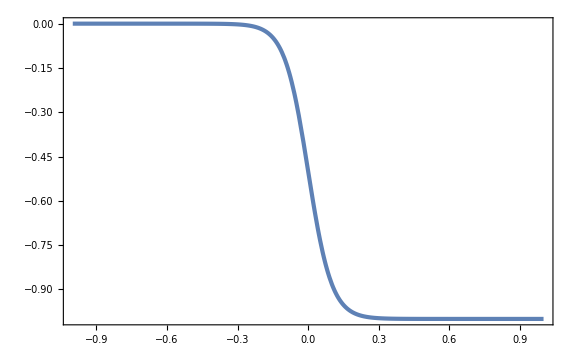

```mathematica
Plot[Vp[x]/.{F0->-1,dx->0.1},{x,-1,1}]
```

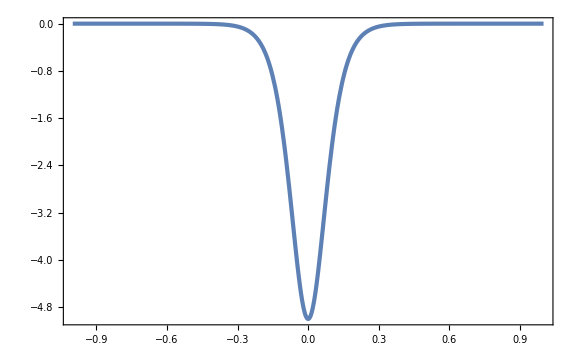

```mathematica
Plot[Vp'[x]/.{F0->-1,dx->0.1},{x,-1,1},PlotRange->Full]
```

```mathematica
Hs=10^-4;
ϵSRs=10^-2;
ASRs=10^-9;
AUSRcs=10^-2;
```

```mathematica
F0s=F0/.Solve[1/2 F0^2/(3 Hs^2)==ASRs&&F0<0,F0][[1]];F0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[10^-2/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

-7.74597×10^-9

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNs=10^-2;
dxs=dotxcs dNs/Hs;dxs//N
```

1.59155×10^-6

```mathematica
params={H->Hs,F0->F0s,dotxL->dotxLs,xL->xLs,dx->dxs};
```

```mathematica
tf=(NLs+3)/Hs;tf//N
```

52632.1

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ϵsol[t_]=dotxsol[t]^2/(2 Hs^2);
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hs dotxsol[t])/.params;
```

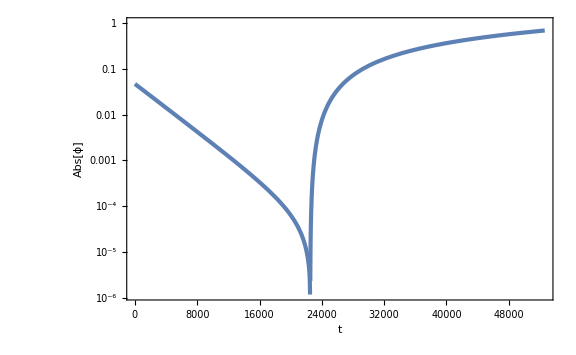

```mathematica
LogPlot[Abs[xsol[t]],{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

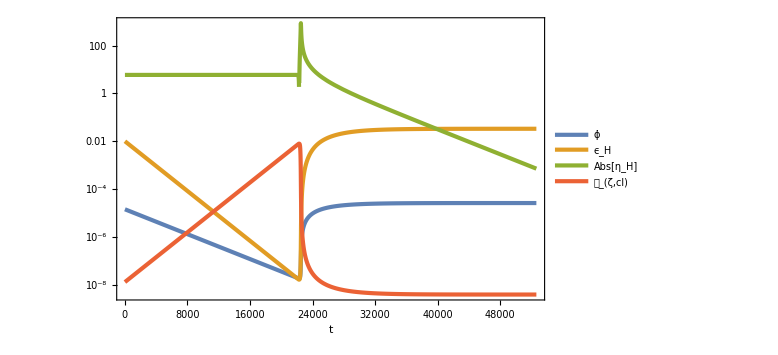

```mathematica
LogPlot[{dotxsol[t],ϵsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hs/(2π))^2},{t,0,tf},PlotRange->Full,PlotLegends->{OverDot[ϕ],Subscript[ϵ, H],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl]},FrameLabel->{t,None}]
```

```mathematica
deltax=Hs/(2π);
```

```mathematica
barsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xbar[t_]=x[t]/.barsol;
dotxbar[t_]=x'[t]/.barsol;
```

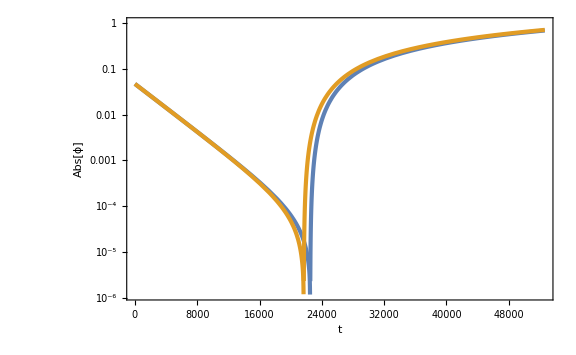

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xbar[t]]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

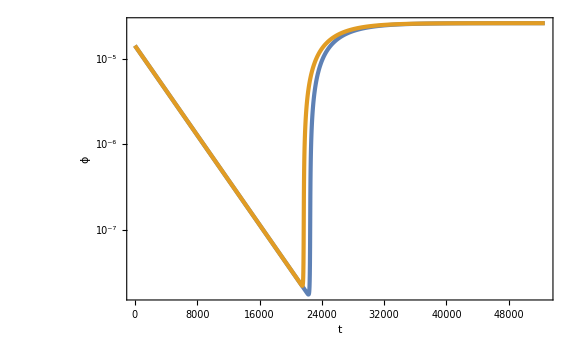

```mathematica
LogPlot[{dotxsol[t],dotxbar[t]},{t,0,tf},FrameLabel->{t,OverDot[ϕ]}]
```

```mathematica
xf=xsol[tf-1/Hs]
```

0.4340526374348987687838267584

```mathematica
ζL=Hs((t/.FindRoot[xbar[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

-0.08301099280070268085393075666

```mathematica
tS=1/Hs;
```

```mathematica
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]];
```

NDSolve::precw: The precision of the differential equation ({{-(√(3/5) (1+Tanh[Times[«3»]]))/200000000+(3 x'[t])/10000+x''[t]==0,x[10000]==-0.0022780177685517181779696572245,x'[10000]==7.04095473290232144184214765×10^-7},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
```

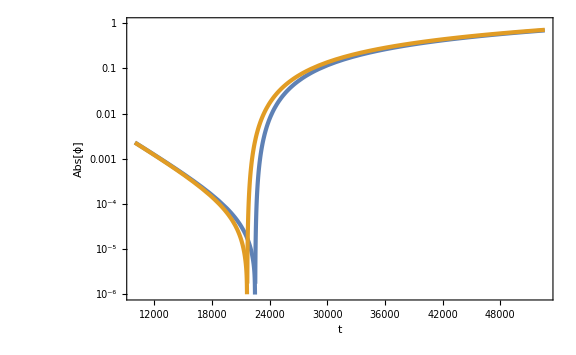

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xSsol[t]]},{t,tS,tf},FrameLabel->{t,Abs[ϕ]}]
```

```mathematica
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1»==0.4340526374348987687838267584) is less than WorkingPrecision (30.).

-0.08301099469433590651472030798

```mathematica
ζS/ζL
```

1.00000002281183686366849609

```mathematica
dotxczetaLPS=ParallelTable[bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Hs((t/.FindRoot[xsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))//Quiet;
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))-ζL//Quiet;
{dotxc,ζL,ζS^2},{i,-1,1,1/10}];//AbsoluteTiming
```

{8.48268,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(2.2751469824419948570978×10^-18)/x^2

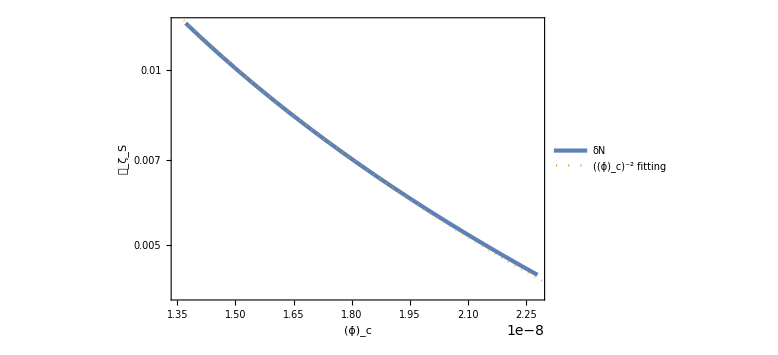

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{Subscript[OverDot[ϕ], "c"],Subscript[𝒫, Subscript[ζ, "S"]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-8,10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[OverDot[ϕ], "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.00689082524014306402145836787

```mathematica
fNL=PSvszetaLint'[0]/PS0
```

5.195401726503492072148772

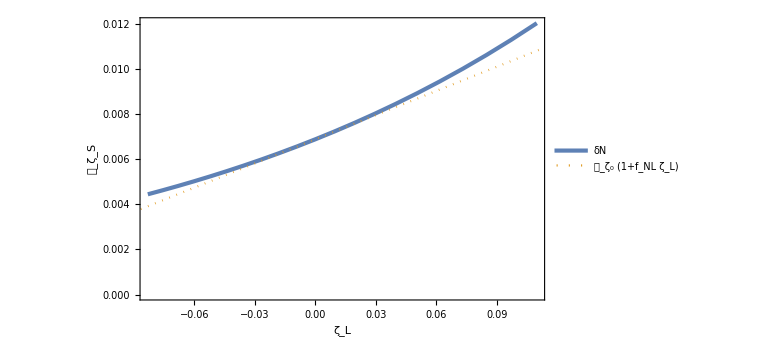

```mathematica
Show[ListPlot[PSvszetaL,FrameLabel->{Subscript[ζ, "L"],Subscript[𝒫, Subscript[ζ, "S"]]},PlotLegends->{Style[δN,Italic]}],Plot[PS0(1+fNL x),{x,-1,1},PlotStyle->{Color[2],Dotted},PlotLegends->{Subscript[𝒫, Subscript[ζ, "S"0]](1+Subscript[f, NL] Subscript[ζ, "L"])}]]
```

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t],x''[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ddotxsol[t_]=x''[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet
dotxc=dotxsol[tc]
```

22342.6825988886125295590267602

1.81952054653249756629981×10^-8

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

-1.94949537400849883383

```mathematica
Zc=NIntegrate[Exp[-3Hs (t-tc)]/dotxsol[t]^2,{t,tc,tf}]
```

2.86593×10^17

```mathematica
1/(3Hs dotxc^2)
```

1.00685009883165822059508×10^19

```mathematica
Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])
```

4.775968781440159215005204024×10^12

```mathematica
Ztildec=1/(3Hs dotxc^2)+Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])+Zc
```

1.03551×10^19

```mathematica
-power/(Hs dotxc^2 Ztildec)
```

5.68662

#### tanh transition (smooth)

```mathematica
Quit[]
```

```mathematica
Vp[x_]=F0/2(1+Tanh[x/dx]);
```

```mathematica
Plot[Vp[x]/.{F0->-1,dx->0.1},{x,-1,1}]
```

-Graphics-

```mathematica
Plot[Vp'[x]/.{F0->-1,dx->0.1},{x,-1,1},PlotRange->Full]
```

-Graphics-

```mathematica
Hs=10^-4;
ϵSRs=10^-2;
ASRs=10^-9;
AUSRcs=10^-2;
```

```mathematica
F0s=F0/.Solve[1/2 F0^2/(3 Hs^2)==ASRs&&F0<0,F0][[1]];F0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[10^-2/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

-7.74597×10^-9

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNs=10;
dxs=dotxcs dNs/Hs;dxs//N
```

0.00159155

```mathematica
params={H->Hs,F0->F0s,dotxL->dotxLs,xL->-3dxs+xLs,dx->dxs};
```

```mathematica
Cp=(-Vp'[0])/(3Hs)/.params;Cp//N
Cm=-3Hs;Cm//N
```

0.00811156

-0.0003

```mathematica
tf=(NLs+2+3)/Hs;tf//N
```

72632.1

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ϵsol[t_]=dotxsol[t]^2/(2 Hs^2);
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hs dotxsol[t])/.params;
```

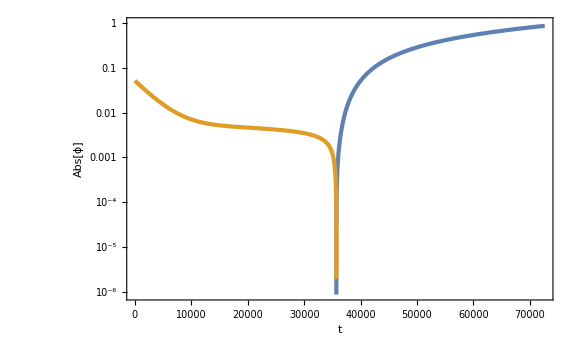

```mathematica
LogPlot[{xsol[t],-xsol[t]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

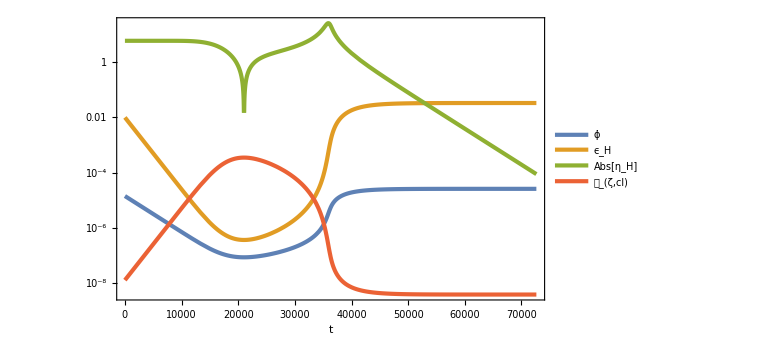

```mathematica
LogPlot[{dotxsol[t],ϵsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hs/(2π))^2},{t,0,tf},PlotRange->Full,PlotLegends->{ϕ̇,Subscript[ϵ, H],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl]},FrameLabel->{t,None}]
```

```mathematica
deltax=Hs/(2π);
```

```mathematica
barsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xbar[t_]=x[t]/.barsol;
dotxbar[t_]=x'[t]/.barsol;
```

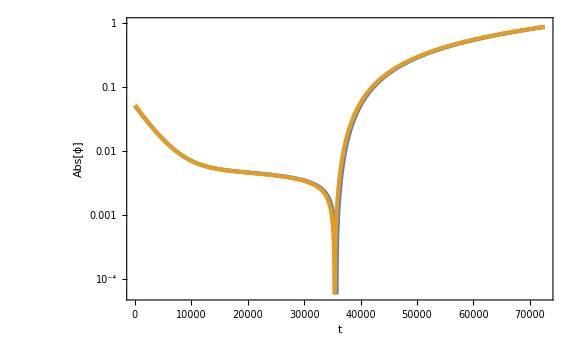

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xbar[t]]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

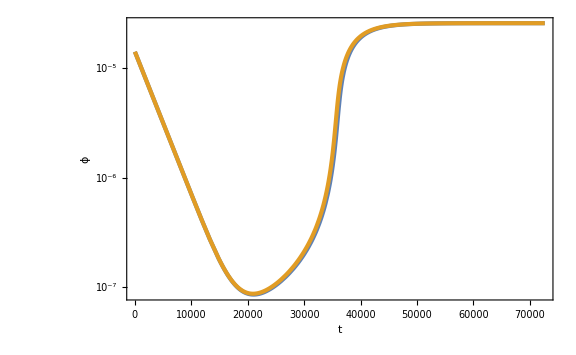

```mathematica
LogPlot[{dotxsol[t],dotxbar[t]},{t,0,tf},FrameLabel->{t,ϕ̇}]
```

```mathematica
xf=xsol[tf-1/Hs]
```

0.61365699454201893113477054563

```mathematica
ζL=Hs((t/.FindRoot[xbar[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1»[t]==0.61365699454201893113477054563) is less than WorkingPrecision (30.).

-0.0295023456476593789750730534

```mathematica
tS=1/Hs;
```

```mathematica
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]];
```

NDSolve::precw: The precision of the differential equation ({{-(√(3/5) (1+Tanh[Times[«3»]]))/200000000+(3 x'[t])/10000+x''[t]==0,x[10000]==-0.0070520745247806800805842837272,x'[10000]==7.04870496738533348527088153×10^-7},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
```

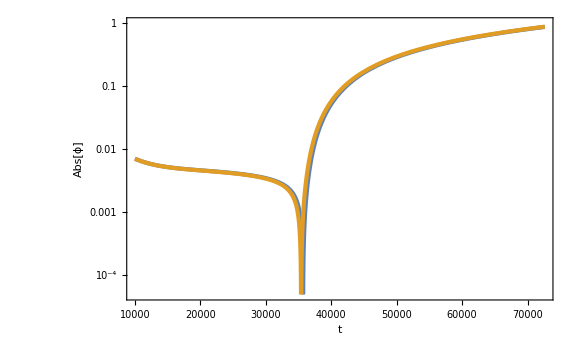

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xSsol[t]]},{t,tS,tf},FrameLabel->{t,Abs[ϕ]}]
```

```mathematica
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

-0.0293917504380982125425312155

```mathematica
ζS/ζL
```

0.996251307916937082592704551

```mathematica
dotxczetaLPS=ParallelTable[bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Hs((t/.FindRoot[xsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))//Quiet;
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))-ζL//Quiet;
{dotxc,ζL,ζS^2},{i,-10,10}];//AbsoluteTiming
```

{6.32519,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(7.392758202447947422783373×10^-18)/x^2

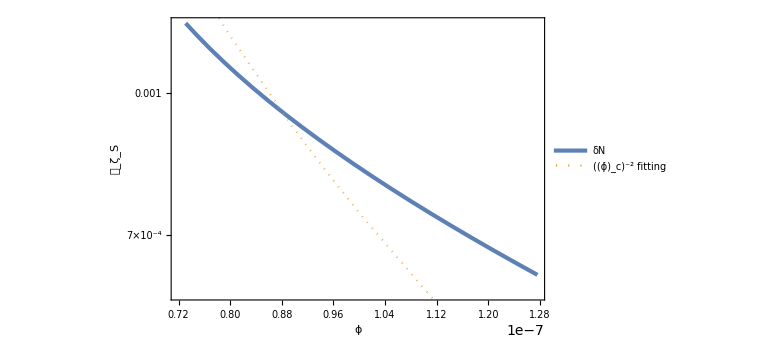

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-8,10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.00086387499381544646892392754

```mathematica
fNL=PSvszetaLint'[0]/PS0
```

1.06854037702752625266004

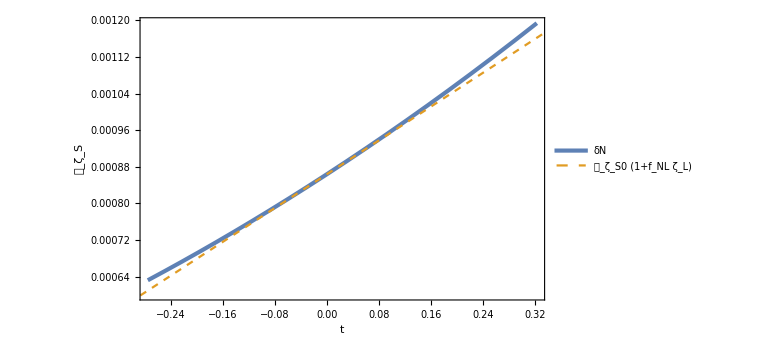

```mathematica
Show[ListPlot[PSvszetaL,FrameLabel->{t,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],Plot[{PS0(1+fNL x)},{x,-1,1},PlotStyle->{{Color[2],Dashed}},PlotLegends->{Subscript[𝒫, Subscript[ζ, S0]](1+Subscript[f, NL] Subscript[ζ, "L"])}]]
```

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t],x''[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ddotxsol[t_]=x''[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==-3dxs,{t,NLs/Hs},WorkingPrecision->30]//Quiet
dotxc=dotxsol[tc]
```

18436.8834694940933692150766359

9.6282866880557489440508056×10^-8

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

-1.1009519594228090841881

```mathematica
Zc=NIntegrate[Exp[-3Hs(t-tc)]/dotxsol[t]^2,{t,tc,tf}]
```

3.84867×10^17

```mathematica
1/(3Hs dotxc^2)
```

3.595677387708396186126241×10^17

```mathematica
Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])
```

2.95465257739263189451541264×10^10

```mathematica
Ztildec=1/(3Hs dotxc^2)+Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])+Zc
```

7.44434×10^17

```mathematica
-power/(Hs dotxc^2 Ztildec)
```

1.59531

#### tanh transition (smooth, early c)

```mathematica
Quit[]
```

```mathematica
Vp[x_]=F0/2(1+Tanh[x/dx]);
```

```mathematica
Plot[Vp[x]/.{F0->-1,dx->0.1},{x,-1,1}]
```

-Graphics-

```mathematica
Plot[Vp'[x]/.{F0->-1,dx->0.1},{x,-1,1},PlotRange->Full]
```

-Graphics-

```mathematica
Hs=10^-4;
ϵSRs=10^-2;
ASRs=10^-9;
AUSRcs=10^-2;
```

```mathematica
F0s=F0/.Solve[1/2 F0^2/(3 Hs^2)==ASRs&&F0<0,F0][[1]];F0s//N
ϵUSRcs=ϵ/.Solve[1/(2ϵ)(Hs/(2π))^2==AUSRcs,ϵ][[1]];ϵUSRcs//N
dotxcs=xdotc/.Solve[xdotc^2/(2 Hs^2)==ϵUSRcs&&xdotc>0,xdotc][[1]];dotxcs//N
NLs=1/6 Log[10^-2/ϵUSRcs];NLs//N
dotxLs=dotxcs Exp[3 NLs];dotxLs//N
xLs=-(dotxLs-dotxcs)/(3Hs)//Simplify;xLs//N
```

-7.74597×10^-9

1.26651×10^-8

1.59155×10^-8

2.26321

0.0000141421

-0.0470874

```mathematica
dNs=10;
dxs=dotxcs dNs/Hs;dxs//N
```

0.00159155

```mathematica
params={H->Hs,F0->F0s,dotxL->dotxLs,xL->-3dxs+xLs,dx->dxs};
```

```mathematica
Cp=(-Vp'[0])/(3Hs)/.params;Cp//N
Cm=-3Hs;Cm//N
```

0.00811156

-0.0003

```mathematica
tf=(NLs+2+3)/Hs;tf//N
```

72632.1

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ϵsol[t_]=dotxsol[t]^2/(2 Hs^2);
ηsol[t_]=-6-2 Vp[xsol[t]]/(Hs dotxsol[t])/.params;
```

```mathematica
LogPlot[{xsol[t],-xsol[t]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

-Graphics-

```mathematica
1/Hs
```

10000

```mathematica
LogPlot[{dotxsol[t],ϵsol[t],Abs[ηsol[t]],1/(2ϵsol[t])(Hs/(2π))^2},{t,0,tf},PlotRange->Full,PlotLegends->{ϕ̇,Subscript[ϵ, H],Abs[Subscript[η, H]],Subscript[𝒫, ζ,cl]},FrameLabel->{t,None}]
```

-Graphics-

```mathematica
deltax=Hs/(2π);
```

```mathematica
barsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

```mathematica
xbar[t_]=x[t]/.barsol;
dotxbar[t_]=x'[t]/.barsol;
```

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xbar[t]]},{t,0,tf},FrameLabel->{t,Abs[ϕ]}]
```

-Graphics-

```mathematica
LogPlot[{dotxsol[t],dotxbar[t]},{t,0,tf},FrameLabel->{t,ϕ̇}]
```

-Graphics-

```mathematica
xf=xsol[tf-1/Hs]
```

0.61365699454201893113477054563

```mathematica
ζL=Hs((t/.FindRoot[xbar[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1»[t]==0.61365699454201893113477054563) is less than WorkingPrecision (30.).

-0.0295023456476593789750730534

```mathematica
tS=1/Hs;
```

```mathematica
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]];
```

NDSolve::precw: The precision of the differential equation ({{-(√(3/5) (1+Tanh[Times[«3»]]))/200000000+(3 x'[t])/10000+x''[t]==0,x[10000]==-0.0070520745247806800805842837272,x'[10000]==7.04870496738533348527088153×10^-7},{},{},{},{}}) is less than WorkingPrecision (30.).

```mathematica
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
```

```mathematica
LogPlot[{Abs[xsol[t]],Abs[xSsol[t]]},{t,tS,tf},FrameLabel->{t,Abs[ϕ]}]
```

-Graphics-

```mathematica
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))
```

FindRoot::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

-0.0293917504380982125425312155

```mathematica
ζS/ζL
```

0.996251307916937082592704551

```mathematica
xc=xsol[1/Hs]
```

-0.0070679900190898696141611721035

```mathematica
xL/.params//N
```

-0.051862

```mathematica
Hs/(2π)//N
```

0.0000159155

```mathematica
dotxczetaLPS=ParallelTable[bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL+i deltax,x'[0]==dotxL}/.params,{x[t],x'[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet;
dotxc=dotxsol[tc];
ζL=Hs((t/.FindRoot[xsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))//Quiet;
Ssol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[tS]==xsol[tS]+deltax,x'[tS]==dotxsol[tS]}/.params,{x[t],x'[t]},{t,tS,tf},WorkingPrecision->30][[1]]//Quiet;
xSsol[t_]=x[t]/.Ssol;
dotxSsol[t_]=x'[t]/.Ssol;
ζS=Hs((t/.FindRoot[xSsol[t]==xf,{t,tf-1/Hs},WorkingPrecision->30])-(tf-1/Hs))-ζL//Quiet;
{dotxc,ζL,ζS^2},{i,-10,10}];//AbsoluteTiming
```

{6.09886,Null}

```mathematica
PSvsdotxc=dotxczetaLPS.Transpose[{{1,0,0},{0,0,1}}];
```

```mathematica
PSfit[x_]=a x^-2/.FindFit[PSvsdotxc,a x^-2,a,x]
```

(4.3980891927516845513174104×10^-16)/x^2

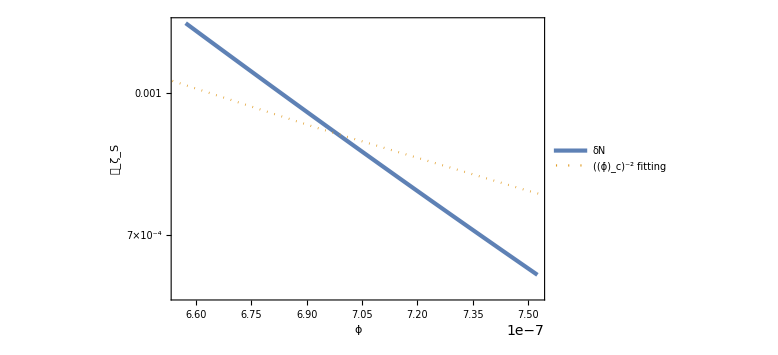

```mathematica
Show[ListLogPlot[PSvsdotxc,FrameLabel->{ϕ̇,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],LogPlot[PSfit[x],{x,10^-7,3 10^-6},PlotStyle->{Color[2],Dotted},PlotLegends->{Row[{Superscript[Subscript[ϕ̇, "c"],-2]," fitting"}]}]]
```

```mathematica
PSvszetaL=dotxczetaLPS.Transpose[{{0,1,0},{0,0,1}}];
```

```mathematica
PSvszetaLint[x_]=Interpolation[PSvszetaL][x];
```

```mathematica
PS0=PSvszetaLint[0]
```

0.00086387499381544646892392754

```mathematica
fNL=PSvszetaLint'[0]/PS0
```

1.06854037702752625266004

```mathematica
Show[ListPlot[PSvszetaL,FrameLabel->{t,Subscript[𝒫, Subscript[ζ, S]]},PlotLegends->{Style[δN,Italic]}],Plot[{PS0(1+fNL x)},{x,-1,1},PlotStyle->{{Color[2],Dashed}},PlotLegends->{Subscript[𝒫, Subscript[ζ, S0]](1+Subscript[f, NL] Subscript[ζ, "L"])}]]
```

-Graphics-

```mathematica
bgsol=NDSolve[{x''[t]+3H x'[t]+Vp[x[t]]==0,x[0]==xL,x'[0]==dotxL}/.params,{x[t],x'[t],x''[t]},{t,0,tf},WorkingPrecision->30][[1]]//Quiet;
xsol[t_]=x[t]/.bgsol;
dotxsol[t_]=x'[t]/.bgsol;
ddotxsol[t_]=x''[t]/.bgsol;
tc=t/.FindRoot[xsol[t]==xc,{t,1/Hs},WorkingPrecision->30]//Quiet
dotxc=dotxsol[tc]
```

10000.

7.0487049673853334852708815×10^-7

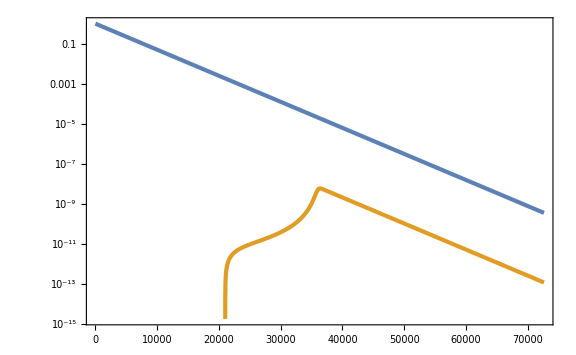

```mathematica
LogPlot[{Exp[-3Hs t],ddotxsol[t]},{t,0,tf}]
```

```mathematica
1/Hs//N
```

10000.

```mathematica
PSvsdotxcint[x_]=Interpolation[PSvsdotxc][x];
```

```mathematica
power=dotxc PSvsdotxcint'[dotxc]/PSvsdotxcint[dotxc]
```

-4.6959508620483684526679

```mathematica
Zc=NIntegrate[Exp[-3Hs (t-tc)]/dotxsol[t]^2,{t,tc,tf}]
```

8.17322×10^16

```mathematica
1/(3Hs dotxc^2)
```

6.7090353362010074952496541×10^15

```mathematica
Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])
```

2.351141899901860325985013393×10^9

```mathematica
Ztildec=1/(3Hs dotxc^2)+Exp[-3Hs(tf-tc)]/(ddotxsol[tf]dotxsol[tf])+Zc
```

8.84412×10^16

```mathematica
-power/(Hs dotxc^2 Ztildec)
```

1.06869

```mathematica
fNL
```

1.06854037702752625266004

### linear slope reparam.

```mathematica
Quit[]
```

```mathematica
xUSR[t_]=x[t]/.DSolve[{x''[t]+3H x'[t]==0,x[tL]==xL,x'[tL]==dotxL},x[t],t][[1]]//Simplify
```

(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
tcUSR=t/.Solve[xUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL-3 H xc+3 H xL)]/(3 H)

```mathematica
xUSR'[tcUSR]//Simplify
```

dotxL+3 H (-xc+xL)

```mathematica
xSR[t_]=Collect[Simplify[x[t]/.DSolve[{x''[t]+3H x'[t]-(√(2ϵ0))/Mpl V0==0,x[tc]==xc,x'[tc]==dotxc},x[t],t][[1]]],{xc,dotxc},Simplify]/.{dotxc->xUSR'[tc],V0->3 Mpl^2 H^2}//Simplify
```

-(dotxL ⅇ^(3 H (-tc+tL)) (-1+ⅇ^(3 H (-t+tc))))/(3 H)+xc+1/3 √2 Mpl (-1+ⅇ^(3 H (-t+tc))+3 H t-3 H tc) √ϵ0

#### Add long-wavelength ptb. as xbar[t]=x[t]+dxL

```mathematica
xbarUSR[t_]=xUSR[t]+dxL
```

dxL+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H xL)/(3 H)

```mathematica
ttbarc=t/.Solve[xbarUSR[t]==xc,t][[1]]/.{C[1]->0}//Simplify
```

tL+Log[dotxL/(dotxL+3 H (dxL-xc+xL))]/(3 H)

```mathematica
xbarSR[t_]=xSR[t]/.{tc->ttbarc}//Simplify
```

xc+(dotxL-dotxL ⅇ^(3 H (-t+tL))+3 H (dxL-xc+xL))/(3 H)+1/3 √2 Mpl √ϵ0 (-1+3 H (t-tL)+(dotxL ⅇ^(3 H (-t+tL)))/(dotxL+3 H (dxL-xc+xL))-Log[dotxL/(dotxL+3 H (dxL-xc+xL))])

#### Find xi0 during SR

xbar[tbar]=x[t] condition at linear both in xi0 and dxL

```mathematica
xi0Eq=Simplify[Simplify[xbarSR[t+δ xi0]==xSR[t]/.{dxL->δ dxL}]/.{tc->tcUSR}]
```

1/3 ((dotxL ⅇ^(3 H (-t+tL)))/H-(dotxL ⅇ^(-3 H (t-tL+xi0 δ)))/H+3 dxL δ-(√2 dotxL ⅇ^(3 H (-t+tL)) Mpl √ϵ0)/(dotxL-3 H xc+3 H xL)+3 √2 H Mpl xi0 δ √ϵ0+(√2 dotxL ⅇ^(-3 H (t-tL+xi0 δ)) Mpl √ϵ0)/(dotxL+3 H (-xc+xL+dxL δ))+√2 Mpl √ϵ0 Log[dotxL/(dotxL-3 H xc+3 H xL)]-√2 Mpl √ϵ0 Log[dotxL/(dotxL+3 H (-xc+xL+dxL δ))])==0

```mathematica
xi0Eqlinear=Normal[Series[xi0Eq,{δ,0,1}]]/.{δ->1}//Simplify
```

dxL+dotxL ⅇ^(3 H (-t+tL)) xi0+√2 H Mpl xi0 √ϵ0+(√2 dxL H Mpl √ϵ0)/(dotxL+3 H (-xc+xL))==(√2 dotxL ⅇ^(3 H (-t+tL)) H Mpl (dxL+xi0 (dotxL+3 H (-xc+xL))) √ϵ0)/(dotxL+3 H (-xc+xL))^2

```mathematica
xi0SR[t_]=xi0/.Simplify[Simplify[Solve[xi0Eqlinear,xi0][[1]]]/.{xc->xL+(dotxL-dotxc)/(3H)}]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

(-dotxc dxL+√2 dxL (-1+ⅇ^(3 H (-t+tc))) H Mpl √ϵ0)/(dotxc (dotxc ⅇ^(3 H (-t+tc))-√2 (-1+ⅇ^(3 H (-t+tc))) H Mpl √ϵ0))

```mathematica
-δ/Limit[xi0SR[t]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]^2 D[Limit[xi0SR[t]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]^2, δ]//Simplify
```

2/(1+δ)

by the way, xi0 during USR is simple

```mathematica
xi0USR[t_]=xi0/.Solve[xbarUSR[t+xi0]==xUSR[t],xi0][[1]]/.{C[1]->0}
```

(-3 H t+3 H tL+Log[dotxL/(dotxL ⅇ^(-3 H (t-tL))+3 dxL H)])/(3 H)

#### Calculate P’s correction

correction disappears during USR at linear in dxL

```mathematica
Simplify[Normal[Series[xUSR'[t]xi0USR'[t]+xUSR''[t]xi0USR[t],{dxL,0,1}]],{H>0,t-tL>0}]
```

0

in SR

```mathematica
Coeff=xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-(3 √2 dxL ⅇ^(3 H (-t+tc)) H^2 Mpl √ϵ0)/dotxc

```mathematica
Normal[Series[Simplify[xSR''[t]xi0SR[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,-1}]]/.{δ->dotxc/(√(2ϵ0)Mpl H)}//Simplify
```

-(3 √2 dxL ⅇ^(3 H (-t+tc)) H^2 Mpl √ϵ0)/dotxc

```mathematica
Simplify[xSR'[t]xi0SR'[t]/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

-(3 dxL ⅇ^(3 H (-t+tc)) H δ)/(1+ⅇ^(3 H (-t+tc)) (-1+δ))

```mathematica
Limit[Simplify[(xSR'[t]xi0SR'[t]+xSR''[t]xi0SR[t])/(xSR''[t]xi0SR[t])/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]
```

1/(1-δ^2)

Finally dxL-dependence of dotxc and dotx is required

```mathematica
ddotxcddxL=D[xbarUSR'[ttbarc]-xUSR[tcUSR],dxL]
```

3 H

```mathematica
ddotxddxL=D[xbarSR'[t]-xSR'[t],dxL]/.{dxL->0}/.{xc->xL+(dotxL-dotxc)/(3H)}//Simplify
```

(3 √2 dotxL ⅇ^(3 H (-t+tL)) H^2 Mpl √ϵ0)/dotxc^2

```mathematica
ddotxcddxL/ddotxddxL//Simplify
```

(dotxc^2 ⅇ^(3 H (t-tL)))/(√2 dotxL H Mpl √ϵ0)

bispectrum correction reads

```mathematica
Coeff ddotxcddxL/ddotxddxL(-2/dotxc Ps)/.{dxL->-dotxc/H zetaL,dotxL->dotxc Exp[3H(tc-tL)]}//Simplify
```

-6 Ps zetaL

```mathematica
Limit[3H dotxc^2 Exp[-3H(t-tc)]/(xSR'[t]xSR''[t])/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{t->∞},Assumptions->{H>0}]
```

-δ^2/(-1+δ)

```mathematica
3H dotxc^2 Integrate[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}//Simplify,{t,tc,∞}]
```

$Aborted

```mathematica
Normal[Series[Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}/.{t->tc+dt}],{dt,0,1}]]
```

1/dotxc^2+(3 dt (dotxc H-2 √2 H^2 Mpl √ϵ0))/dotxc^3

```mathematica
Solve[1==3dt(dotxc H-2 √(2ϵ0)Mpl H^2)/dotxc,dt]
```

{{dt→-dotxc/(3 H (-dotxc+2 √2 H Mpl √ϵ0))}}

```mathematica
dtanal=Normal[Series[dt/.Solve[1==3dt(dotxc H-2 √(2ϵ0)Mpl H^2)/dotxc,dt][[1]]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,1}]]/.{δ->dotxc/(√(2ϵ0)Mpl H)}
```

-dotxc/(6 √2 H^2 Mpl √ϵ0)

```mathematica
Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]
```

ⅇ^(3 H (t-tc))/((dotxc+√2 (-1+ⅇ^(3 H (t-tc))) H Mpl √ϵ0)^2)

```mathematica
Normal[Series[Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,1}]]
```

ⅇ^(3 H (t-tc))/(2 (-1+ⅇ^(3 H (t-tc)))^2 H^2 Mpl^2 ϵ0)-(ⅇ^(3 H (t-tc)) δ)/((-1+ⅇ^(3 H (t-tc)))^3 H^2 Mpl^2 ϵ0)

```mathematica
Normal[Series[Normal[Series[Simplify[Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify,{δ,0,1}]]/.{t->tc+dt}//Simplify,{dt,0,1}]]
```

(-1-δ)/(24 H^2 Mpl^2 ϵ0)-δ/(27 dt^3 H^5 Mpl^2 ϵ0)+(dt δ)/(80 H Mpl^2 ϵ0)+(1+δ)/(18 dt^2 H^4 Mpl^2 ϵ0)

```mathematica
Zcanal[δ_]=3H dotxc^2 dtanal/dotxc^2/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

-δ/2

```mathematica
Zcintegrand[δ_]=Simplify[3H dotxc^2 Exp[-3H(t-tc)]/xSR'[t]^2/.{dotxL->dotxc Exp[3H(tc-tL)]}]/.{dotxc->δ √(2ϵ0)Mpl H}//Simplify
```

(3 ⅇ^(3 H (t-tc)) H δ^2)/((-1+ⅇ^(3 H (t-tc))+δ)^2)

```mathematica
Integrate[Zcintegrand[δ],t]/.{t->tc}
```

-δ

```mathematica
Zc[δ_]=Limit[Integrate[Zcintegrand[δ],t],{t->∞},Assumptions->{H>0}]-Integrate[Zcintegrand[δ],t]/.{t->tc}
```

δ